```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
SetOptions[ListLogPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];psifactor[k_]=(Cos[x]^k)*(Sin[x]^(Np-k))*Sqrt[(k!)*((Np-k)!)]^(M-2);
norm=Sum[psifactor[k]^2,{k,0,Np}];
```

```mathematica
Np=50;M=3;
Sz=Sum[(2*k-Np)*psifactor[k]^2,{k,0,Np}]/norm;
Sx=0;
Sy=0;
VarSz=Sum[(2*k-Np)^2*psifactor[k]^2,{k,0,Np}]/norm-Sz^2;
VarSx=Sum[k*(Np-k+1)*psifactor[k]^2,{k,0,Np}]/norm+Sum[(k+1)*(Np-k)*psifactor[k]^2,{k,0,Np}]/norm-Sx^2;
CovSzSz=Sum[(2*k-Np)^2*psifactor[k]^2,{k,0,Np}]/norm-Sz^2;
CorSzSz=CovSzSz/Sqrt[VarSz*VarSz];
```

General::munfl: 0.0000320891^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^72 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^74 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

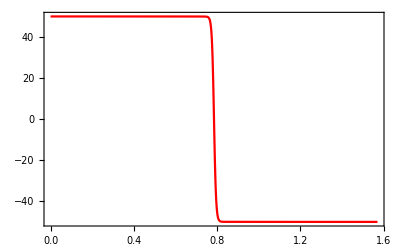

General::munfl: 0.0000320891^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^72 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^74 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

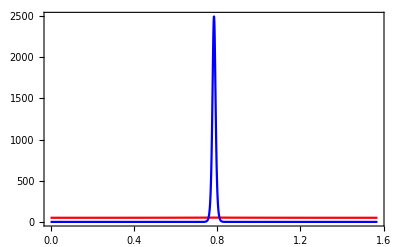

General::munfl: 0.0000320891^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^72 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^74 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

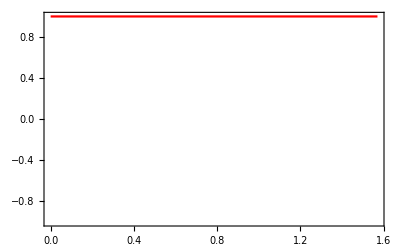

```mathematica
Plot[Sz,{x,0,Pi/2},PlotStyle->Red]
Plot[{VarSx,VarSz},{x,0,Pi/2},PlotStyle->{Red,Blue},PlotRange->All]
Plot[CorSzSz,{x,0,Pi/2},PlotStyle->Red]
```

```mathematica
VarSx/.x->Pi/4.0
VarSz/.x->Pi/4.0
```

52.0894

2495.82